# 07. Waveform Parameterisations and Window Envelopes

## PiecewiseConstant, Fourier, FourierSine, Chebyshev, B-Splines, custom BasisMatrix, Hann/Blackman envelopes, singular-value conditioning, and Q-space ADMM.

## 0. Setup and Loading SpinDynamica

Add the SpinDynamica package directory to $Path by searching upward from the notebook directory and load SpinDynamica`. All five OptimalControl` subpackages load automatically. Reuses reduced-basis examples from Tutorial02 and Tutorial08 (Manual Chapter 11).

```mathematica
Module[{dir = Quiet[Check[NotebookDirectory[], Directory[]]], found = None},
  Do[If[FileExistsQ[FileNameJoin[{dir, "SpinDynamica", "SpinDynamica.m"}]],
      found = FileNameJoin[{dir, "SpinDynamica"}]; Break[]];
    dir = ParentDirectory[dir], {6}];
  If[found === None && FileExistsQ[FileNameJoin[{Directory[], "SpinDynamica", "SpinDynamica.m"}]],
    found = FileNameJoin[{Directory[], "SpinDynamica"}]];
  If[StringQ[found] && !MemberQ[$Path, found], PrependTo[$Path, found]];
];
Needs["SpinDynamica`"];
<|"Version" -> $SpinDynamicaVersion, "OptimalControlContexts" -> Select[$Packages, StringStartsQ[#, "OptimalControl`"] &]|>
```

SpinDynamica version SDv3.10.3b3 (modified by Google Anti-Gravity Neon) loaded by Mathematica 14.3 running on Microsoft Windows (64-bit).

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator,Duration,Exp,Expand,Plus,Power,Simplify,SolidAngle,Times,WignerD}

<|Version→SDv3.10.3b3 (modified by Google Anti-Gravity Neon),OptimalControlContexts→{OptimalControl`Visualization`,OptimalControl`TimeOptimal`,OptimalControl`SecondOrderOptimizers`,OptimalControl`Optimizers`,OptimalControl`Ensemble`,OptimalControl`GRAPE`,OptimalControl`Objectives`,OptimalControl`Kernels`}|>

## Introduction

Piecewise-constant control allows each time slice an independent amplitude, which can generate high-frequency slice-to-slice oscillations exceeding probe resonator bandwidths. Linearly expanding u(t) = B . p across smooth orthogonal polynomials, Fourier harmonics, or locally supported B-splines (optionally multiplied by an envelope window vanishing cleanly at t = 0 and t = T) reduces search dimensionality and guarantees smooth hardware pulses.

Construct and compare PiecewiseConstant, Fourier, FourierSine, Chebyshev, BSpline, and BasisMatrix representations.

Inspect basis-function shapes, window tapering (Hann, Hamming, Blackman), and singular-value spectra of B via BuildControlBasis.

Understand how SpinDynamica uses thin-SVD Q-space reduction when constrained smooth bases encounter hard disk or slew bounds.

Compare waveform smoothness and Fourier spectra interactively.

## Mathematical Background

At normalised slice midpoints tau_j = t_{mid,j}/T in (0, 1), BuildControlBasis[spec, dtVec, window] constructs B = diag(w) B_raw in R^{Nt x P}, mapping reduced coefficients P_coeff in R^{P x M} linearly via u = B . P_coeff. Exact gradients pull back via the chain rule as grad_P = B^T . grad_u.

When a windowed spline basis is combined with AmplitudeNormBound or SlewRateBound, tiny edge window weights cause B^T B to have condition number kappa ~ 10^5. SpinDynamica avoids ill-conditioning by computing thin SVD B = Q R (Q^T Q = I_r) and executing proximal ADMM steps directly inside isometric Q-space before inverting back to P_coeff.

## Worked Example

Compare five basis parameterisations on the off-resonance single-spin pi/2_x gate (+60 Hz offset, 10 ms, 40 slices), plus constrained Hann-windowed cubic B-splines under joint circular disk and slew bounds via Q-space ADMM.

```mathematica
SetSpinSystem[1];
b1 = ZeemanBasis[];
uPi2 = MatrixExp[-I (Pi/2.) Normal[MatrixRepresentation[opI[1, "x"], b1]]];
pRef[spec_, win_: None, extraOpts___Rule] := GRAPEOptimize[
  60. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2], {0.01, 40},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  ControlParameterization -> spec, ControlWindow -> win,
  TargetFidelity -> 0.9999, MaxIterations -> 120, RandomSeed -> 19, extraOpts];

rPWC = pRef["PiecewiseConstant"];
rFour = pRef[{"Fourier", 5}];
rFSin = pRef[{"FourierSine", 8}];
rCheb = pRef[{"Chebyshev", 8}];
rBS = pRef[{"BSpline", 10}, "Hann"];
(* Custom Gaussian-modulated Legendre/Chebyshev basis matrix via {"BasisMatrix", mat} *)
customMat = Transpose[Table[Exp[-4. ((j - 20.5)/20.)^2] * LegendreP[m, (j - 20.5)/20.], {m, 0, 6}, {j, 40}]];
rCust = pRef[{"BasisMatrix", customMat}, "Hann"];
rConBS = pRef[{"BSpline", 12}, "Hann", AmplitudeNormBound -> 120., SlewRateBound -> 40000.];

AssociationMap[Function[r, <|"ParamsShape" -> Dimensions[r["Parameters"]], "Fidelity" -> r["FinalFidelity"], "Iters" -> r["Iterations"]|>],
  <|"PiecewiseConstant" -> rPWC, "Fourier(5)" -> rFour, "FourierSine(8)" -> rFSin,
    "Chebyshev(8)" -> rCheb, "HannBSpline(10)" -> rBS, "CustomBasis(7)" -> rCust, "HannBSpline_QADMM" -> rConBS|>]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

<|ParamsShape→{1},Fidelity→(HannBSpline_QADMM→OptimalControlResult[…])[FinalFidelity],Iters→(HannBSpline_QADMM→OptimalControlResult[…])[Iterations]|>

Plot the constrained Hann-windowed cubic B-spline solution next to the PiecewiseConstant solution:

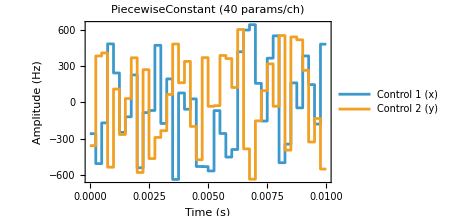
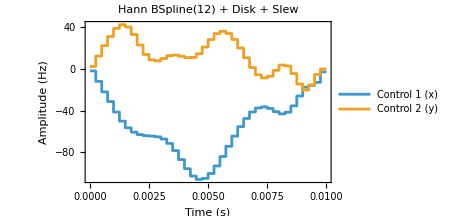
-Graphics- | -Graphics-

```mathematica
Grid[{{
  PlotOptimalControlWaveform[rPWC, PlotLabel -> "PiecewiseConstant (40 params/ch)", ImageSize -> 350],
  PlotOptimalControlWaveform[rConBS, PlotLabel -> "Hann BSpline(12) + Disk + Slew", ImageSize -> 350]
}}]
```

## Interactive Exploration

Lab 7A is an instant BuildControlBasis anatomy explorer: vary basis family, parameter budget P, B-spline degree, slice count Nt, and envelope window to inspect columns of B = diag(w) B_raw alongside the singular-value spectrum and condition number kappa(B) in real time.

```mathematica
renderLab7A[family_String, nParam_Integer, bsDeg_Integer, nt_Integer, winName_String] := Module[
  {dtVec, winOpt, spec, bas, B, colsToPlot, svals, condNum, pCols, pSV},
  dtVec = ConstantArray[0.01 / nt, nt];
  winOpt = If[winName === "None", None, winName];
  spec = Switch[family,
    "Fourier", {"Fourier", Max[1, Quotient[nParam, 2]]},
    "FourierSine", {"FourierSine", Max[1, nParam]},
    "Chebyshev", {"Chebyshev", Max[1, nParam - 1]},
    _, {"BSpline", Max[2, nParam], Min[bsDeg, Max[1, nParam - 1]]}
  ];
  bas = BuildControlBasis[spec, dtVec, winOpt];
  B = bas["BasisMatrix"];
  colsToPlot = Transpose[B][[;; Min[6, bas["NumParams"]]]];
  svals = SingularValueList[B, Tolerance -> 0];
  condNum = Max[svals] / Max[Min[svals], 10^-15];
  pCols = ListLinePlot[colsToPlot, Frame -> True, FrameLabel -> {"Slice Index j", "B_{j,p}"},
    PlotLabel -> "First 6 Basis Columns (P = " <> ToString[bas["NumParams"]] <> ")", ImageSize -> 330];
  pSV = ListLogPlot[Max[#, 10^-15] & /@ svals, Joined -> True, Mesh -> All, Frame -> True,
    FrameLabel -> {"Mode Index", "Singular Value sigma_i"}, PlotRange -> All,
    PlotLabel -> "Singular Values (kappa = " <> ToString[ScientificForm[condNum, 3]] <> ")", ImageSize -> 310];
  Column[{
    Row[{"Spec: ", spec, "   Window: ", winName, "   B dims: ", Dimensions[B], "   IsIdentityQ: ", bas["IsIdentityQ"]}],
    Row[{pCols, " ", pSV}]
  }]
];

runLab7B[family_String, nParam_Integer, winName_String, useCon_] := Module[
  {b, uPi2, winOpt, spec, extra, res, specFreq},
  SetSpinSystem[1]; b = ZeemanBasis[];
  uPi2 = MatrixExp[-I (Pi/2.) Normal[MatrixRepresentation[opI[1, "x"], b]]];
  winOpt = If[winName === "None", None, winName];
  spec = Switch[family,
    "Fourier", {"Fourier", Max[1, Quotient[nParam, 2]]},
    "FourierSine", {"FourierSine", Max[1, nParam]},
    "Chebyshev", {"Chebyshev", Max[1, nParam - 1]},
    _, {"BSpline", Max[2, nParam]}
  ];
  extra = If[TrueQ[useCon], {AmplitudeNormBound -> 120., SlewRateBound -> 40000.}, {}];
  res = GRAPEOptimize[60. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2],
    {0.01, 40}, FrequencyUnits -> "Hz", ControlUnits -> "Hz",
    ControlParameterization -> spec, ControlWindow -> winOpt,
    TargetFidelity -> 0.9999, MaxIterations -> 130, RandomSeed -> 19, Sequence @@ extra];
  specFreq = Abs[Fourier[res["Controls"][[All, 1]] + I res["Controls"][[All, 2]]]];
  <|"Result" -> res, "Spec" -> spec, "Win" -> winName, "Constrained" -> TrueQ[useCon], "FFT" -> specFreq|>
];

renderLab7B[d_Association] := Module[{res = d["Result"]},
  Column[{
    Panel[Row[{"Spec = ", d["Spec"], "   Win = ", d["Win"], "   F_U = ", NumberForm[res["FinalFidelity"], 6],
      "   Opt = ", res["Optimizer"], "   Params/ch = ", First[Dimensions[res["Parameters"]]],
      "   Viol = ", ScientificForm[res["MaxConstraintViolation"], 2]}]],
    Row[{
      PlotOptimalControlWaveform[res, ImageSize -> 340],
      ListPlot[Take[d["FFT"], 20], Filling -> Axis, Joined -> True, Frame -> True,
        FrameLabel -> {"DFT Bin", "|FFT(ux + i uy)|"}, PlotLabel -> "RF Spectral Bandwidth", ImageSize -> 300]
    }]
  }]
];

lab7BDefault = runLab7B["BSpline", 12, "Hann", True];
lab7BDefault["Result"]["FinalFidelity"]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

0.999983

```mathematica
Manipulate[
  renderLab7A[family, nParam, bsDeg, nt, winName],
  {{family, "BSpline", "Basis Family"}, {"BSpline", "Fourier", "FourierSine", "Chebyshev"}},
  {{nParam, 10, "Param Target P"}, 4, 16, 1, Appearance -> "Labeled"},
  {{bsDeg, 3, "B-Spline Degree"}, {1, 2, 3}},
  {{nt, 40, "Slices Nt"}, {20, 40, 60}},
  {{winName, "Hann", "Envelope Window"}, {"None", "Hann", "Hamming", "Blackman"}}
]
```

Lab 7B runs parameterised GRAPE optimisation on demand (including constrained Hann/Blackman Q-space ADMM when Disk + Slew is checked) and displays both time-domain and DFT spectral bandwidth:

```mathematica
DynamicModule[{family = "BSpline", nParam = 12, winName = "Hann", useCon = True, data = lab7BDefault},
  Panel[Column[{
    Grid[{
      {"Basis Family", SetterBar[Dynamic[family], {"BSpline", "Fourier", "FourierSine", "Chebyshev"}]},
      {"Param Target P", Row[{Slider[Dynamic[nParam], {4, 16, 1}], " ", Dynamic[nParam]}]},
      {"Envelope Window", SetterBar[Dynamic[winName], {"None", "Hann", "Hamming", "Blackman"}]},
      {"Hard Limits", Row[{Checkbox[Dynamic[useCon]], " AmplitudeNormBound 120 Hz + SlewRateBound 40 kHz/s (Q-space ADMM)"}]}
    }, Alignment -> Left],
    Button["Run Parameterised GRAPE", data = runLab7B[family, nParam, winName, useCon], Method -> "Queued"],
    Dynamic[renderLab7B[data]]
  }]]
]
```

## Suggested Experiments

1. Visualise window conditioning: In Lab 7A with BSpline (P = 12), switch Envelope Window from None to Hann and notice how singular values at edges plummet by ~10^4 (explaining why thin-SVD Q-space ADMM is indispensable).

2. Natural zero endpoints without windowing: Test FourierSine vs Hann + BSpline for vanishing turn-on and turn-off RF amplitudes.

3. Spectral bandwidth narrowing: In Lab 7B, lower Param Target P from 16 down to 4 on Fourier or BSpline and compare both F_U and the DFT spectral tail.

4. Toggle Hard Limits on/off under Hann + BSpline and confirm Optimizer switches smoothly to FISTA while maintaining zero boundary amplitude.

## Summary

Reduced waveform parameterisations cut degrees of freedom, smoothly shape pulse transients, and suppress spectral sidebands while preserving exact adjoint gradients. Combining windows with thin-SVD Q-space reduction keeps hard circular disk and slew limits accurate even for highly ill-conditioned spline bases.

Return to 00_OptimalControl_Tutorials_Index.nb or consult the executable CLI fixture (Tutorial02_Universal90Rotation.wls, Tutorial08_ConstrainedRFPulseDesign.wls) and Manual Ch. 11.